#### [Calc] Deriving this Wigner distribution using linearity of Wigner transform in density operators

W1ecat  = 1/Norm[W_(α,Coh.)+W_(-α ,Coh.)+W_(+-)+W_(-+)]

W_(+-)=1/(2π)∫_(-∞)^∞ ⅇ^-ⅈpy ψ_α(x+y/2) ψ_-α*(x-y/2) ⅆy (Wikipedia convention)

```mathematica
ψ[x0_,p0_,x_]:=1/π^(1/4)ⅇ^(ⅈ p0 x)ⅇ^((-(x- x0)^2)/2)ⅇ^(-(ⅈ x0 p0)/2); (* Coherent state wave function *)
Ws1s2[α_,θ_,x_,p_,s1_,s2_]:=FullSimplify[1/(2π)∫_(-∞)^∞ ⅇ^(-ⅈ p y)ψ[s1 √2 α Cos[θ],s1 √2 α Sin[θ],x-y/2]ψ[s2 √2 α Cos[θ],-s2 √2 α Sin[θ],x+y/2]ⅆy];
Ws1s2[α,θ,x,p,1,1]
Ws1s2[α,θ,x,p,-1,-1]
```

(ⅇ^(-p^2-x^2-2 α^2+2 √2 α (x Cos[θ]-p Sin[θ])))/π

(ⅇ^(-p^2-x^2-2 α^2+2 √2 α (-x Cos[θ]+p Sin[θ])))/π

```mathematica
FullSimplify[(Ws1s2[α,θ,x,p,1,1]+Ws1s2[α,θ,x,p,-1,-1])]
FullSimplify[(Ws1s2[α,θ,x,p,1,-1]+Ws1s2[α,θ,x,p,-1,1])]
```

(2 ⅇ^(-p^2-x^2-2 α^2) Cosh[2 √2 α (x Cos[θ]-p Sin[θ])])/π

(2 ⅇ^(-p^2-x^2) Cos[2 √2 α (p Cos[θ]+x Sin[θ])])/π

```mathematica
Wcat[α_,θ_,x_,p_,s_]:=( (2 ⅇ^(-p^2-x^2-2 α^2) Cosh[2 √2 α (x Cos[θ]-p Sin[θ])])/π+s(2 ⅇ^(-p^2-x^2) Cos[2 √2 α (p Cos[θ]+x Sin[θ])])/π)1/(2(1+s ⅇ^(-2 α^2)));
```

#### [Calc] Finding the Wigner distribution after heterodyne heralding

```mathematica
(* 
   For the current example, Wigner distribution has a form: W^(2)=1/𝒩(W_(++)+W_(--)+W_(+-)+W_(-+)).
First, we are interested in finding W_(++,--,+-,--) separately.

 Careful about using the wavefunction for coherent state here. Imaginary part ⅈrα is important.
 For conjugate: use ψ*(x0,p0;x)-> ψ(x0,-p0;x)
*)
```

```mathematica
W2modes1s2[t_,r_,α_,θ_,x1_,p1_,x2_,p2_,s1_,s2_]:=Ws1s2[ t α,θ,x1,p1,s1,s2]Ws1s2[r α,θ+π/2,x2,p2,s1,s2];
```

```mathematica
(* ++ and -- terms for two modes *)
```

```mathematica
W2modes1s2[t,r,α,θ,x1,p1,x2,p2,1,1]+W2modes1s2[t,r,α,θ,x1,p1,x2,p2,-1,-1]
```

```mathematica
(ⅇ^(-p1^2-p2^2-x1^2-x2^2-2 r^2 α^2-2 t^2 α^2))/π^2(ⅇ^(+2 √2 t α (x1 Cos[θ]-p1 Sin[θ])-2 √2 r α (p2 Cos[θ]+x2 Sin[θ]))+ⅇ^(+2 √2 t α (-x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p2 Cos[θ]+x2 Sin[θ])))
```

```mathematica
FullSimplify[(ⅇ^(+2 √2 t α (x1 Cos[θ]-p1 Sin[θ])-2 √2 r α (p2 Cos[θ]+x2 Sin[θ]))+ⅇ^(+2 √2 t α (-x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p2 Cos[θ]+x2 Sin[θ]))),{r^2+t^2==1}]
```

2 Cosh[2 √2 α ((p2 r-t x1) Cos[θ]+(p1 t+r x2) Sin[θ])]

```mathematica
(* final form w_(++)+w_(--) *)
```

```mathematica
(ⅇ^(-p1^2-p2^2-x1^2-x2^2-2 α^2))/π^2 2 Cosh[2 √2 α ((p2 r-t x1) Cos[θ]+(p1 t+r x2) Sin[θ])]
```

```mathematica
(* +- and -+ terms for two modes *)
```

```mathematica
W2modes1s2[t,r,α,θ,x1,p1,x2,p2,1,-1]+W2modes1s2[t,r,α,θ,x1,p1,x2,p2,-1,1]
```

```mathematica
(ⅇ^(-p1^2-p2^2-x1^2-x2^2))/π^2(ⅇ^(-2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])-2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))+ⅇ^(+2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])+2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ])))
```

```mathematica
FullSimplify[(ⅇ^(-2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])-2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))+ⅇ^(+2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])+2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))),{r^2+t^2==1}]
```

2 Cos[2 √2 α ((p1 t+r x2) Cos[θ]+(-p2 r+t x1) Sin[θ])]

```mathematica
(* final form w_(+-)+w_(-+) *)
```

```mathematica
(ⅇ^(-p1^2-p2^2-x1^2-x2^2))/π^2 2 Cos[2 √2 α ((p1 t+r x2) Cos[θ]+(-p2 r+t x1) Sin[θ])]
```

```mathematica
(* General cat two mode B={{t, ⅈ r},{ⅈ r, t}} *)
(* Two-mode Wigner distribution just before heralding *)
W2mode[t_,r_,α_,θ_,x1_,p1_,x2_,p2_,s_]:=(ⅇ^(-p1^2-p2^2-x1^2-x2^2))/(π^2 2(1+s ⅇ^(-2 α^2)))2 (ⅇ^(-2 α^2)Cosh[2 √2 α ((p2 r-t x1) Cos[θ]+(p1 t+r x2) Sin[θ])]+s Cos[2 √2 α ((p1 t+r x2) Cos[θ]+(-p2 r+t x1) Sin[θ])]);
```

```mathematica
(* Gaussian Integrals *)
```

```mathematica
ClearAll[xmat];
xmat[x_,p_]:=Table[x^(i-1)p^(j-1),{i,1,3},{j,1,3}];
Mmat={{a,b,c},{d,e,0(*f*)},{g,(*h*)0,(*i*)0}};
Quiet[ⅇ^Total[Mmat*xmat[x,p],2]]
```

ⅇ^(a+b p+c p^2+d x+e p x+g x^2)

```mathematica
∫_(-∞)^∞ ⅇ^Total[Mmat*xmat,2] ⅆx
```

ConditionalExpression[(ⅇ^((-d^2-2 d p (e+f p)+4 a (g+p (h+i p))+p (4 b (g+p (h+i p))+p (-e^2-2 e f p-f^2 p^2+4 c (g+p (h+i p)))))/(4 (g+p (h+i p)))) √π)/(√(-g-p (h+i p))), Re[g+p (h+i p)]<0]

```mathematica
Collect[-d^2-2 d p (e+f p)+4 a (g+p (h+i p))+p (4 b (g+p (h+i p))+p (-e^2-2 e f p-f^2 p^2+4 c (g+p (h+i p)))),{p,p^2}]
```

-d^2+4 a g+(-2 d e+4 b g+4 a h) p+(-e^2-2 d f+4 c g+4 b h+4 a i) p^2+(-2 e f+4 c h+4 b i) p^3+(-f^2+4 c i) p^4

```mathematica
Expand[((ⅇ^((-d^2+4 a g+(-2 d e+4 b g+4 a h) p+(-e^2-2 d f+4 c g+4 b h+4 a i) p^2+(-2 e f+4 c h+4 b i) p^3+(-f^2+4 c i) p^4)/(4 (g+p h+i p^2))) √π)/(√(-g-p (h+i p))))/.{f->0,h->0,i->0}]
```

-(ⅇ^(a-d^2/(4 g)+((-2 d e+4 b g) p)/(4 g)+((-e^2+4 c g) p^2)/(4 g)) √-g √π)/g

```mathematica
∫_(-∞)^∞ (-(ⅇ^(a-d^2/(4 g)+((-2 d e+4 b g) p)/(4 g)+((-e^2+4 c g) p^2)/(4 g)) √-g √π)/g)ⅆp
```

ConditionalExpression[(2 ⅇ^((c d^2-b d e+a e^2+b^2 g-4 a c g)/(e^2-4 c g)) π)/(√(-4 c+e^2/g) √-g), Re[-4 c+e^2/g]>0]

```mathematica
Quiet[{{a,b,c},{d,e,0(*f*)},{g,(*h*)0,(*i*)0}}=Table[M[[i,j]],{i,1,3},{j,1,3}]];
```

```mathematica
(2 ⅇ^((c d^2-b d e+a e^2+b^2 g-4 a c g)/(e^2-4 c g)) π)/(√(-4 c+e^2/g) √-g)
```

(2 ⅇ^((M⟦1,3⟧ M⟦2,1⟧^2-M⟦1,2⟧ M⟦2,1⟧ M⟦2,2⟧+M⟦1,1⟧ M⟦2,2⟧^2+M⟦1,2⟧^2 M⟦3,1⟧-4 M⟦1,1⟧ M⟦1,3⟧ M⟦3,1⟧)/(M⟦2,2⟧^2-4 M⟦1,3⟧ M⟦3,1⟧)) π)/(√(-4 M⟦1,3⟧+M⟦2,2⟧^2/M⟦3,1⟧) √(-M⟦3,1⟧))

```mathematica
GaussianIntegral[M_]:=(2 ⅇ^((M⟦1,3⟧ M⟦2,1⟧^2-M⟦1,2⟧ M⟦2,1⟧ M⟦2,2⟧+M⟦1,1⟧ M⟦2,2⟧^2+M⟦1,2⟧^2 M⟦3,1⟧-4 M⟦1,1⟧ M⟦1,3⟧ M⟦3,1⟧)/(M⟦2,2⟧^2-4 M⟦1,3⟧ M⟦3,1⟧)) π)/(√(-4 M⟦1,3⟧+M⟦2,2⟧^2/M⟦3,1⟧) √(-M⟦3,1⟧));
ExpCoefficientsToMatrix[expr_,x_,p_]:=CoefficientList[Exponent[expr,ⅇ],{x,p},{3,3}];

(* Trunated Gaussian integrals
∫_(-Δ/2)^(Δ/2) ⅇ^(c x^2+b x +a)ⅆx*)
TruncatedGaussInt[v_,Δ_]:=(ⅇ^(v⟦1⟧-v⟦2⟧^2/(4 v⟦3⟧)) √π (-Erfi[(v⟦2⟧-Δ v⟦3⟧)/(2 √v⟦3⟧)]+Erfi[(v⟦2⟧+Δ v⟦3⟧)/(2 √v⟦3⟧)]))/(2 √v⟦3⟧);
```

#### [Calc] Gaussian filtering

```mathematica
(* ∫_(-∞)^∞ ∫_(-∞)^∞ (1/(π ϵ)ⅇ^(-1/ϵ(x^2+x2^2-2x x2+p^2+p2^2-2p p2)))W2mode[t,r,α,θ,x1,p1,x2,p2,s]ⅆp2ⅆx2 *)(*1/(π^3 ϵ)∫_(-∞)^∞ ⅇ^(-(p^2-2 p p2+x^2-2 x x2+x2^2+p1^2 ϵ+x1^2 ϵ+x2^2 ϵ+p2^2 (1+ϵ))/ϵ)(ⅇ^(-2 α^2)(ⅇ^(+2 √2 t α (x1 Cos[θ]-p1 Sin[θ])-2 √2 r α (p2 Cos[θ]+x2 Sin[θ]))+ⅇ^(+2 √2 t α (-x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p2 Cos[θ]+x2 Sin[θ])))+s(ⅇ^(-2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])-2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))+ⅇ^(+2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])+2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))))ⅆp2 *)
```

```mathematica
ClearAll[v,expr];
expr=ⅇ^(-(p^2-2 p p2+x^2-2 x x2+x2^2+p1^2 ϵ+x1^2 ϵ+x2^2 ϵ+p2^2 (1+ϵ))/ϵ);
v=ExpCoefficientsToMatrix[expr,x2,p2];
v//MatrixForm
```

(-p1^2-x1^2-p^2/ϵ-x^2/ϵ | (2 p)/ϵ | -(1+ϵ)/ϵ
(2 x)/ϵ | 0 | 0
-1-1/ϵ | 0 | 0)

```mathematica
ClearAll[w,expr];
W=1/(π^3 ϵ){ⅇ^(-2 α^2),ⅇ^(-2 α^2),s,s};
expr[1]=ⅇ^(+2 √2 t α (x1 Cos[θ]-p1 Sin[θ])-2 √2 r α (p2 Cos[θ]+x2 Sin[θ]));
expr[2]=ⅇ^(+2 √2 t α (-x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p2 Cos[θ]+x2 Sin[θ]));
expr[3]=ⅇ^(-2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])-2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]));
expr[4]=ⅇ^(+2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])+2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]));
(w[#]=ExpCoefficientsToMatrix[expr[#],x2,p2])&/@Range[4];
```

```mathematica
Simplify[∑_(i=1)^4 W[[i]]GaussianIntegral[v+w[i]]]/.{x->x2,p->p2}
```

1/(π^2 (1+ϵ))ⅇ^(-2 α^2) (ⅇ^(-(p1^2+p2^2+x1^2+x2^2+p1^2 ϵ+x1^2 ϵ-2 r^2 α^2 ϵ-2 √2 α (p2 r-t x1 (1+ϵ)) Cos[θ]-2 √2 α (r x2+p1 t (1+ϵ)) Sin[θ])/(1+ϵ))+ⅇ^(-(p1^2+p2^2+x1^2+x2^2+p1^2 ϵ+x1^2 ϵ-2 r^2 α^2 ϵ+2 √2 α (p2 r-t x1 (1+ϵ)) Cos[θ]+2 √2 α (r x2+p1 t (1+ϵ)) Sin[θ])/(1+ϵ))+ⅇ^(-(p1^2+p2^2+x1^2+x2^2-2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 r^2 α^2 ϵ+2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]-2 ⅈ √2 α (p2 r-t x1 (1+ϵ)) Sin[θ])/(1+ϵ)) s+ⅇ^(-(p1^2+p2^2+x1^2+x2^2-2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 r^2 α^2 ϵ-2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]+2 ⅈ √2 α (p2 r-t x1 (1+ϵ)) Sin[θ])/(1+ϵ)) s)

#### [Calc] Checking normalization

```mathematica
(* Tracing over mode 2 *)
```

```mathematica
ClearAll[w,expr];
W=1/(π^2 (1+ϵ))ⅇ^(-2 α^2){1,1,s,s};
expr[1]=
ⅇ^(-(p1^2+p2^2+x1^2+x2^2+p1^2 ϵ+x1^2 ϵ-2 r^2 α^2 ϵ-2 √2 α (p2 r-t x1 (1+ϵ)) Cos[θ]-2 √2 α (r x2+p1 t (1+ϵ)) Sin[θ])/(1+ϵ));
expr[2]=ⅇ^(-(p1^2+p2^2+x1^2+x2^2+p1^2 ϵ+x1^2 ϵ-2 r^2 α^2 ϵ+2 √2 α (p2 r-t x1 (1+ϵ)) Cos[θ]+2 √2 α (r x2+p1 t (1+ϵ)) Sin[θ])/(1+ϵ));
expr[3]=ⅇ^(-(p1^2+p2^2+x1^2+x2^2-2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 r^2 α^2 ϵ+2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]-2 ⅈ √2 α (p2 r-t x1 (1+ϵ)) Sin[θ])/(1+ϵ));
expr[4]=ⅇ^(-(p1^2+p2^2+x1^2+x2^2-2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 r^2 α^2 ϵ-2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]+2 ⅈ √2 α (p2 r-t x1 (1+ϵ)) Sin[θ])/(1+ϵ));
(w[#]=ExpCoefficientsToMatrix[expr[#],x2,p2])&/@Range[4];
Expand[∑_(i=1)^4 W[[i]]GaussianIntegral[w[i]]]
```

1/π ⅇ^(-2 α^2-1/4 (1+ϵ)^2 (-(8 r^2 α^2 Cos[θ]^2)/(1+ϵ)^3-(8 r^2 α^2 Sin[θ]^2)/(1+ϵ)^3-(4 (-p1^2/(1+ϵ)-x1^2/(1+ϵ)-(p1^2 ϵ)/(1+ϵ)-(x1^2 ϵ)/(1+ϵ)+(2 r^2 α^2 ϵ)/(1+ϵ)+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]))/(1+ϵ)^2))+1/π ⅇ^(-2 α^2-1/4 (1+ϵ)^2 (-(8 r^2 α^2 Cos[θ]^2)/(1+ϵ)^3-(8 r^2 α^2 Sin[θ]^2)/(1+ϵ)^3-(4 (-p1^2/(1+ϵ)-x1^2/(1+ϵ)-(p1^2 ϵ)/(1+ϵ)-(x1^2 ϵ)/(1+ϵ)+(2 r^2 α^2 ϵ)/(1+ϵ)-2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ]))/(1+ϵ)^2))+1/π ⅇ^(-2 α^2-1/4 (1+ϵ)^2 ((8 r^2 α^2 Cos[θ]^2)/(1+ϵ)^3+(8 r^2 α^2 Sin[θ]^2)/(1+ϵ)^3-(4 (-p1^2/(1+ϵ)-x1^2/(1+ϵ)+(2 α^2)/(1+ϵ)-(p1^2 ϵ)/(1+ϵ)-(x1^2 ϵ)/(1+ϵ)+(2 α^2 ϵ)/(1+ϵ)-(2 r^2 α^2 ϵ)/(1+ϵ)-2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ]))/(1+ϵ)^2)) s+1/π ⅇ^(-2 α^2-1/4 (1+ϵ)^2 ((8 r^2 α^2 Cos[θ]^2)/(1+ϵ)^3+(8 r^2 α^2 Sin[θ]^2)/(1+ϵ)^3-(4 (-p1^2/(1+ϵ)-x1^2/(1+ϵ)+(2 α^2)/(1+ϵ)-(p1^2 ϵ)/(1+ϵ)-(x1^2 ϵ)/(1+ϵ)+(2 α^2 ϵ)/(1+ϵ)-(2 r^2 α^2 ϵ)/(1+ϵ)+2 ⅈ √2 p1 t α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]))/(1+ϵ)^2)) s

```mathematica
(* Tracing over mode 1 *)
```

```mathematica
W=1/π{1,1,s,s};
expr[1]=ⅇ^(-2 α^2-1/4 (1+ϵ)^2 (-(8 r^2 α^2 Cos[θ]^2)/(1+ϵ)^3-(8 r^2 α^2 Sin[θ]^2)/(1+ϵ)^3-(4 (-p1^2/(1+ϵ)-x1^2/(1+ϵ)-(p1^2 ϵ)/(1+ϵ)-(x1^2 ϵ)/(1+ϵ)+(2 r^2 α^2 ϵ)/(1+ϵ)+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]))/(1+ϵ)^2));
expr[2]=ⅇ^(-2 α^2-1/4 (1+ϵ)^2 (-(8 r^2 α^2 Cos[θ]^2)/(1+ϵ)^3-(8 r^2 α^2 Sin[θ]^2)/(1+ϵ)^3-(4 (-p1^2/(1+ϵ)-x1^2/(1+ϵ)-(p1^2 ϵ)/(1+ϵ)-(x1^2 ϵ)/(1+ϵ)+(2 r^2 α^2 ϵ)/(1+ϵ)-2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ]))/(1+ϵ)^2));
expr[3]=ⅇ^(-2 α^2-1/4 (1+ϵ)^2 ((8 r^2 α^2 Cos[θ]^2)/(1+ϵ)^3+(8 r^2 α^2 Sin[θ]^2)/(1+ϵ)^3-(4 (-p1^2/(1+ϵ)-x1^2/(1+ϵ)+(2 α^2)/(1+ϵ)-(p1^2 ϵ)/(1+ϵ)-(x1^2 ϵ)/(1+ϵ)+(2 α^2 ϵ)/(1+ϵ)-(2 r^2 α^2 ϵ)/(1+ϵ)-2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ]))/(1+ϵ)^2));
expr[4]=ⅇ^(-2 α^2-1/4 (1+ϵ)^2 ((8 r^2 α^2 Cos[θ]^2)/(1+ϵ)^3+(8 r^2 α^2 Sin[θ]^2)/(1+ϵ)^3-(4 (-p1^2/(1+ϵ)-x1^2/(1+ϵ)+(2 α^2)/(1+ϵ)-(p1^2 ϵ)/(1+ϵ)-(x1^2 ϵ)/(1+ϵ)+(2 α^2 ϵ)/(1+ϵ)-(2 r^2 α^2 ϵ)/(1+ϵ)+2 ⅈ √2 p1 t α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]))/(1+ϵ)^2));
(w[#]=ExpCoefficientsToMatrix[expr[#],x1,p1])&/@Range[4];
Simplify[∑_(i=1)^4 W[[i]]GaussianIntegral[w[i]],r^2==1-t^2]
```

2+2 ⅇ^(-2 α^2) s

#### [Rslt] “ϵ/2” Gaussian Filtered 2 mode normalized Wigner

```mathematica
(* ∫_(-∞)^∞ ∫_(-∞)^∞ (1/(π ϵ)ⅇ^(-1/ϵ(x^2+x2^2-2x x2+p^2+p2^2-2p p2)))W2mode[t,r,α,θ,x1,p1,x,p,s]ⅆpⅆx *)
Wn[ϵ_,t_,r_,α_,θ_,x1_,p1_,x2_,p2_,s_]:=1/(2(1+s ⅇ^(-2 α^2)))1/(π^2 (1+ϵ))ⅇ^(-2 α^2) (ⅇ^(-(p1^2+p2^2+x1^2+x2^2+p1^2 ϵ+x1^2 ϵ-2 r^2 α^2 ϵ-2 √2 α (p2 r-t x1 (1+ϵ)) Cos[θ]-2 √2 α (r x2+p1 t (1+ϵ)) Sin[θ])/(1+ϵ))+ⅇ^(-(p1^2+p2^2+x1^2+x2^2+p1^2 ϵ+x1^2 ϵ-2 r^2 α^2 ϵ+2 √2 α (p2 r-t x1 (1+ϵ)) Cos[θ]+2 √2 α (r x2+p1 t (1+ϵ)) Sin[θ])/(1+ϵ))+ⅇ^(-(p1^2+p2^2+x1^2+x2^2-2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 r^2 α^2 ϵ+2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]-2 ⅈ √2 α (p2 r-t x1 (1+ϵ)) Sin[θ])/(1+ϵ)) s+ⅇ^(-(p1^2+p2^2+x1^2+x2^2-2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 r^2 α^2 ϵ-2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]+2 ⅈ √2 α (p2 r-t x1 (1+ϵ)) Sin[θ])/(1+ϵ)) s);
```

```mathematica
Wn[2,t,r,α,θ,x1,p1,x2,p2,s](* comparing to Wh from Wigner Cat-v3.nb *)
```

1/(6 π^2 (1+ⅇ^(-2 α^2) s))ⅇ^(-2 α^2) (ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2-x2^2+4 r^2 α^2-2 √2 (p2 r-3 t x1) α Cos[θ]-2 √2 (3 p1 t+r x2) α Sin[θ]))+ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2-x2^2+4 r^2 α^2+2 √2 (p2 r-3 t x1) α Cos[θ]+2 √2 (3 p1 t+r x2) α Sin[θ]))+ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2-x2^2+6 α^2-4 r^2 α^2+2 ⅈ √2 (3 p1 t+r x2) α Cos[θ]-2 ⅈ √2 (p2 r-3 t x1) α Sin[θ])) s+ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2-x2^2+6 α^2-4 r^2 α^2-2 ⅈ √2 (3 p1 t+r x2) α Cos[θ]+2 ⅈ √2 (p2 r-3 t x1) α Sin[θ])) s)

```mathematica
Simplify[%-1/(2(1+s ⅇ^(-2 α^2)))(s 1/(3 π^2)ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2-x2^2-4 r^2 α^2+2 ⅈ √2 (3 p1 t+r x2) α Cos[θ]-2 ⅈ √2 (p2 r-3 t x1) α Sin[θ]))+s 1/(3 π^2)ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2-x2^2-4 r^2 α^2-2 ⅈ √2 (3 p1 t+r x2) α Cos[θ]+2 ⅈ √2 (p2 r-3 t x1) α Sin[θ]))+1/(3 π^2)ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2-x2^2-6 α^2+4 r^2 α^2-2 √2 (p2 r-3 t x1) α Cos[θ]-2 √2 (3 p1 t+r x2) α Sin[θ]))+1/(3 π^2)ⅇ^(1/3 (-3 p1^2-p2^2-3 x1^2-x2^2-6 α^2+4 r^2 α^2+2 √2 (p2 r-3 t x1) α Cos[θ]+2 √2 (3 p1 t+r x2) α Sin[θ])))]
```

0

```mathematica
(* Matches the result for ϵ = 2 *)
```

#### [Calc] Heralding on Δ range in x_2 around the origin (after Gaussian filtering)

```mathematica
(* Leaving out the pre factor for now *)
```

```mathematica
Simplify[∫_(-Δp/2)^(Δp/2) (1/(2(1+s ⅇ^(-2 α^2)))1/(π^2 (1+ϵ))ⅇ^(-2 α^2) (ⅇ^(-(p1^2+p2^2+x1^2+x2^2+p1^2 ϵ+x1^2 ϵ-2 r^2 α^2 ϵ-2 √2 α (p2 r-t x1 (1+ϵ)) Cos[θ]-2 √2 α (r x2+p1 t (1+ϵ)) Sin[θ])/(1+ϵ))+ⅇ^(-(p1^2+p2^2+x1^2+x2^2+p1^2 ϵ+x1^2 ϵ-2 r^2 α^2 ϵ+2 √2 α (p2 r-t x1 (1+ϵ)) Cos[θ]+2 √2 α (r x2+p1 t (1+ϵ)) Sin[θ])/(1+ϵ))+ⅇ^(-(p1^2+p2^2+x1^2+x2^2-2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 r^2 α^2 ϵ+2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]-2 ⅈ √2 α (p2 r-t x1 (1+ϵ)) Sin[θ])/(1+ϵ)) s+ⅇ^(-(p1^2+p2^2+x1^2+x2^2-2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 r^2 α^2 ϵ-2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]+2 ⅈ √2 α (p2 r-t x1 (1+ϵ)) Sin[θ])/(1+ϵ)) s))ⅆp2,r^2==1-t^2]
```

(ⅇ^(-(p1^2+x1^2+x2^2+α^2+p1^2 ϵ+x1^2 ϵ+2 α^2 ϵ-α^2 Cos[2 θ]+t^2 α^2 (-1-2 ϵ+Cos[2 θ])+2 √2 r x2 α (ⅈ Cos[θ]+Sin[θ])+2 √2 t (p1+ⅈ x1) α (1+ϵ) (ⅈ Cos[θ]+Sin[θ]))/(1+ϵ)) (ⅇ^(-(2 α ((-1+t^2) α (1+2 ϵ)+√2 (-ⅈ r x2+t (-ⅈ p1+2 x1) (1+ϵ)) Cos[θ]-√2 (2 r x2+t (2 p1+ⅈ x1) (1+ϵ)) Sin[θ]))/(1+ϵ)) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))])+ⅇ^(-(2 α ((-1+t^2) α (1+2 ϵ)-ⅈ √2 (r x2+p1 t (1+ϵ)) Cos[θ]-ⅈ √2 t x1 (1+ϵ) Sin[θ]))/(1+ϵ)) (-Erf[(-Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))])+ⅇ^((2 α (α+α ϵ+√2 r x2 (2 ⅈ Cos[θ]+Sin[θ])+√2 t (1+ϵ) ((2 ⅈ p1-x1) Cos[θ]+(p1+2 ⅈ x1) Sin[θ])))/(1+ϵ)) s (-Erf[(-Δp/2+ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])+ⅇ^((2 α (α+α ϵ+√2 r x2 Sin[θ]-√2 t (1+ϵ) (x1 Cos[θ]-p1 Sin[θ])))/(1+ϵ)) s (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])))/(4 π^(3/2) (ⅇ^(2 α^2)+s) √(1+ϵ))

```mathematica
expr[0]=ⅇ^(-(p1^2+x1^2+x2^2+α^2+p1^2 ϵ+x1^2 ϵ+2 α^2 ϵ-α^2 Cos[2 θ]+t^2 α^2 (-1-2 ϵ+Cos[2 θ])+2 √2 r x2 α (ⅈ Cos[θ]+Sin[θ])+2 √2 t (p1+ⅈ x1) α (1+ϵ) (ⅈ Cos[θ]+Sin[θ]))/(1+ϵ));
expr[1]=ⅇ^(-(2 α ((-1+t^2) α (1+2 ϵ)+√2 (-ⅈ r x2+t (-ⅈ p1+2 x1) (1+ϵ)) Cos[θ]-√2 (2 r x2+t (2 p1+ⅈ x1) (1+ϵ)) Sin[θ]))/(1+ϵ));
expr[2]=ⅇ^(-(2 α ((-1+t^2) α (1+2 ϵ)-ⅈ √2 (r x2+p1 t (1+ϵ)) Cos[θ]-ⅈ √2 t x1 (1+ϵ) Sin[θ]))/(1+ϵ));
expr[3]=ⅇ^((2 α (α+α ϵ+√2 r x2 (2 ⅈ Cos[θ]+Sin[θ])+√2 t (1+ϵ) ((2 ⅈ p1-x1) Cos[θ]+(p1+2 ⅈ x1) Sin[θ])))/(1+ϵ));
expr[4]=ⅇ^((2 α (α+α ϵ+√2 r x2 Sin[θ]-√2 t (1+ϵ) (x1 Cos[θ]-p1 Sin[θ])))/(1+ϵ));(expr[#]=Exp[Simplify[Exponent[expr[0],ⅇ]+Exponent[expr[#],ⅇ]]])&/@Range[4];
(w[#]=CoefficientList[Collect[Exponent[expr[#],ⅇ],{x2}],{x2},{3}])&/@Range[4];
W=1/(4 π^(3/2) (ⅇ^(2 α^2)+s) √(1+ϵ)){
(Erf[(Δp/2-√2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]),
(Erf[(Δp/2-√2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]),
s(Erf[(Δp/2-ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δp/2+ⅈ √2 r α Sin[θ])/(√(1+ϵ))]),
s(Erf[(Δp/2-ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δp/2+ⅈ √2 r α Sin[θ])/(√(1+ϵ))])};
```

```mathematica
∑_(i=1)^4 W[[i]]TruncatedGaussInt[w[i],Δx]
```

```mathematica
Simplify[Expand[%]]
```

(ⅇ^(-(x1^2-α^2+t^2 α^2+x1^2 ϵ+2 t^2 α^2 ϵ+p1^2 (1+ϵ)+(-1+t^2) α^2 Cos[2 θ])/(1+ϵ)) ((ⅇ^((2 α (-ⅈ √2 p1 t (1+ϵ) Cos[θ]-r^2 α Cos[θ]^2+t (t α (1+2 ϵ)-ⅈ √2 x1 (1+ϵ) Sin[θ])))/(1+ϵ))+ⅇ^((2 α (ⅈ √2 p1 t (1+ϵ) Cos[θ]-r^2 α Cos[θ]^2+t (t α (1+2 ϵ)+ⅈ √2 x1 (1+ϵ) Sin[θ])))/(1+ϵ))) s Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))] (Erfi[1/2 √(-1/(1+ϵ)) (Δx-2 ⅈ √2 r α Cos[θ])]+Erfi[1/2 √(-1/(1+ϵ)) (Δx+2 ⅈ √2 r α Cos[θ])])+(ⅇ^((2 α (-ⅈ √2 p1 t (1+ϵ) Cos[θ]-r^2 α Cos[θ]^2+t (t α (1+2 ϵ)-ⅈ √2 x1 (1+ϵ) Sin[θ])))/(1+ϵ))+ⅇ^((2 α (ⅈ √2 p1 t (1+ϵ) Cos[θ]-r^2 α Cos[θ]^2+t (t α (1+2 ϵ)+ⅈ √2 x1 (1+ϵ) Sin[θ])))/(1+ϵ))) s Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))] (Erfi[1/2 √(-1/(1+ϵ)) (Δx-2 ⅈ √2 r α Cos[θ])]+Erfi[1/2 √(-1/(1+ϵ)) (Δx+2 ⅈ √2 r α Cos[θ])])+(ⅇ^((2 α (α ϵ+√2 t x1 (1+ϵ) Cos[θ]-√2 p1 t (1+ϵ) Sin[θ]+r^2 α Sin[θ]^2))/(1+ϵ))+ⅇ^((2 α (α ϵ-√2 t x1 (1+ϵ) Cos[θ]+√2 p1 t (1+ϵ) Sin[θ]+r^2 α Sin[θ]^2))/(1+ϵ))) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erfi[1/2 √(-1/(1+ϵ)) (Δx-2 √2 r α Sin[θ])]+Erfi[1/2 √(-1/(1+ϵ)) (Δx+2 √2 r α Sin[θ])])))/(8 π (ⅇ^(2 α^2)+s) √(-1/(1+ϵ)) √(1+ϵ))

#### [Rslt] Unnormalized Heterodyned Wigner

```mathematica
WunHetero[t_,r_,α_,θ_,x1_,p1_,Δx_,Δp_,ϵ_,s_]:=(ⅇ^(-2 α^2))/(8π(1+s ⅇ^(-2 α^2)))  ((ⅇ^(-p1^2-x1^2+2 r^2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]) +ⅇ^(-p1^2-x1^2+2 r^2 α^2-2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ]) ) (Erf[(Δx/2+√2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δx/2-√2 r α Sin[θ])/(√(1+ϵ))])(Erf[(Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δp/2-√2 r α Cos[θ])/(√(1+ϵ))])+(ⅇ^(-p1^2-x1^2+2 t^2 α^2+2 ⅈ √2 p1 t α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]) +ⅇ^(-p1^2-x1^2+2 t^2 α^2-2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ]) )s (Erf[(Δx/2+ ⅈ √2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δx/2- ⅈ √2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δp/2+ ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δp/2-ⅈ √2 r α Sin[θ])/(√(1+ϵ))]));
ClearAll[expr,w,W];
expr[1]=ⅇ^(-p1^2-x1^2+2 r^2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]);
expr[2]=ⅇ^(-p1^2-x1^2+2 r^2 α^2-2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ]);
expr[3]=ⅇ^(-p1^2-x1^2+2 t^2 α^2+2 ⅈ √2 p1 t α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]);
expr[4]=ⅇ^(-p1^2-x1^2+2 t^2 α^2-2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ]);
(w[#]=ExpCoefficientsToMatrix[expr[#],x1,p1])&/@Range[4];
W=(ⅇ^(-2 α^2))/(8π(1+s ⅇ^(-2 α^2))){(Erf[(Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δp/2-√2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δx/2+√2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δx/2-√2 r α Sin[θ])/(√(1+ϵ))]),(Erf[(Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δp/2-√2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δx/2+√2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δx/2-√2 r α Sin[θ])/(√(1+ϵ))]),s (Erf[(Δx/2+ ⅈ √2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δx/2- ⅈ √2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δp/2+ ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δp/2-ⅈ √2 r α Sin[θ])/(√(1+ϵ))]),s (Erf[(Δx/2+ ⅈ √2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δx/2- ⅈ √2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δp/2+ ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δp/2-ⅈ √2 r α Sin[θ])/(√(1+ϵ))])};
```

```mathematica
(* Probability of success *)
Simplify[Distribute[Simplify[∑_(i=1)^4 W[[i]]GaussianIntegral[w[i]],r^2==1-t^2]]]
```

1/(4 (ⅇ^(2 α^2)+s))(s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])+ⅇ^(2 α^2) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))]))

#### [Calc] η Threshold

```mathematica
(* For threshold - use calcs from Wigner Cat -v2.nb and iPad: Cat via noisy Threshold ZPS *)
```

```mathematica
ClearAll[V,Vfunc,v];
Vfunc[μ_,s_]:=(ⅇ^(t^2 α^2))/(2π)s^μ(FullSimplify[Cosh[α^2(1- η )r^2]+(-1)^μ Sinh[α^2(1- η )r^2]]/(ⅇ^(α^2(1- η r^2))+s ⅇ^(-α^2(1- η r^2))));
V[s_]:={Vfunc[0,s],Vfunc[0,s],Vfunc[1,s],Vfunc[1,s]};

expr[1]=ⅇ^(-p1^2-x1^2-2 t^2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]);
expr[2]=ⅇ^(-p1^2-x1^2-2 t^2 α^2-2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ]);
expr[3]=ⅇ^(-p1^2-x1^2+2 ⅈ √2 p1 t α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]);
expr[4]=ⅇ^(-p1^2-x1^2-2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ]);
(v[#]=ExpCoefficientsToMatrix[expr[#],x1,p1])&/@Range[4];
```

#### [Rslt] Wigner distributions - essential code (General cat)

```mathematica
ClearAll[WunHetero];
WunHetero[t_,r_,α_,θ_,x1_,p1_,Δx_,Δp_,ϵ_,s_]:=(ⅇ^(-2 α^2))/(4π(1+s ⅇ^(-2 α^2)))   ⅇ^(-p1^2-x1^2)(ⅇ^(2 r^2 α^2) Cosh[2 √2 t α (x1 Cos[θ]-p1 Sin[θ])](Erf[(Δp/2-√2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δx/2-√2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δx/2+√2 r α Sin[θ])/(√(1+ϵ))])+ ⅇ^(2 t^2 α^2) Cos[2 √2 t α (p1 Cos[θ]+x1 Sin[θ])]s (Erf[(Δx/2-ⅈ √2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δx/2+ⅈ √2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δp/2-ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δp/2+ⅈ √2 r α Sin[θ])/(√(1+ϵ))]));PsHetero[t_,r_,α_,θ_,Δx_,Δp_,ϵ_,s_]:= (ⅇ^(-2 α^2))/(4(1+s ⅇ^(-2 α^2)))(s (Erf[(Δx/2-ⅈ √2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δx/2+ⅈ √2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δp/2-ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δp/2+ⅈ √2 r α Sin[θ])/(√(1+ϵ))])+ⅇ^(2 α^2) (Erf[(Δp/2-√2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δx/2-√2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δx/2+√2 r α Sin[θ])/(√(1+ϵ))]));

WnHetero[t_,r_,α_,θ_,x1_,p1_,Δx_,Δp_,ϵ_,s_]:=Re[WunHetero[t,r,α,θ,x1,p1,Δx,Δp,ϵ,s]/PsHetero[t,r,α,θ,Δx,Δp,ϵ,s]];
Wcat[α_,θ_,x_,p_,s_]:=( (2 ⅇ^(-p^2-x^2-2 α^2) Cosh[2 √2 α (x Cos[θ]-p Sin[θ])])/π+s(2 ⅇ^(-p^2-x^2) Cos[2 √2 α (p Cos[θ]+x Sin[θ])])/π)1/(2(1+s ⅇ^(-2 α^2)));(* Typo in https://arxiv.org/pdf/2006.16985.pdf Eq. (27) *)
(* Results for the threshold detectors obtained from iPad *)

WnThreshold[t_,α_,θ_,x1_,p1_,η_,s_]:=((Exp[(1-η)(1-t^2)α^2]- s Exp[-(1-η)(1-t^2)α^2])/(Exp[α^2(1-η (1-t^2))]+s Exp[-α^2(1-η (1-t^2))]))Sinh[t^2 α^2]Wcat[t α,θ,x1,p1,-1]+((Exp[(1-η)(1-t^2)α^2]+ s Exp[-(1-η)(1-t^2)α^2])/(Exp[α^2(1-η (1-t^2))]+s Exp[-α^2(1-η (1-t^2))]))Cosh[t^2 α^2]Wcat[t α,θ,x1,p1,1];
PsThreshold[t_,α_,η_,s_]:=(Exp[α^2(1-η (1-t^2))]+s Exp[-α^2(1-η (1-t^2))])/(Exp[α^2]+s Exp[-α^2]);
PsηRelativeImprovement[t_,r_,α_,θ_,Δx_,Δp_,ϵ_,η_,s_]:=Re[(PsHetero[t,r,α,θ,Δx,Δp,ϵ,s]-PsThreshold[t,α,η,s])/PsThreshold[t,α,η,s]];
(*
Fidelity:
(2π)/Ps[t,r,α,θ,Δ,Δp,s]∑_(i=1)^4 ∑_(j=1)^4 V[s][[i]]W[[j]]int[v[i],w[j]];

ηPurity:
2π∑_(i=1)^4 ∑_(j=1)^4 V[s][[i]]V[s][[j]]int[v[i],v[j]];

*)
(* Fidelity calcs FullSimplify[Simplify[Collect[(2π)/PsHetero[t,r,α,θ,Δx,Δp,ϵ,s]∑_(i=1)^4 ∑_(j=1)^4 V[s][[i]]W[[j]]GaussianIntegral[v[i]+w[j]],{η,Δx,Δp}],r^2==1-t^2]]
((2 ⅇ^(2 α^2 (1+t^2 η)) s+ⅇ^(2 α^2 η) s^2+ⅇ^(2 α^2 (2 t^2+η)) s^2)(Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])+(ⅇ^(2 α^2 (2+t^2 (-2+η)))+ⅇ^(2 α^2 (2+t^2 η))+2 ⅇ^(2 α^2 (1+η)) s) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))]))
(* Purity of η Threshold *)Simplify[2π∑_(i=1)^4 ∑_(j=1)^4 V[s][[i]]V[s][[j]]GaussianIntegral[v[i]+v[j]]]*)
ηPurity[t_,r_,α_,θ_,η_,s_]:=(1+ⅇ^(4 (-1+r^2) α^2)+4 ⅇ^(2 α^2 (-1+r^2 η)) s+ⅇ^(4 r^2 α^2 (-1+η)) s^2+ⅇ^(4 α^2 (-1+r^2 η)) s^2)/(2 (1+ⅇ^(2 α^2 (-1+r^2 η)) s)^2);
(*subs1:={Erf[(Δx/2-√2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δx/2+√2 r α Sin[θ])/(√(1+ϵ))]->Ax, 
Erf[(Δp/2-√2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]->Ap,
Erf[(Δx/2-ⅈ √2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δx/2+ⅈ √2 r α Cos[θ])/(√(1+ϵ))] ->Bx,
Erf[(Δp/2-ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δp/2+ⅈ √2 r α Sin[θ])/(√(1+ϵ))]->Bp};
subs2:={Ap Ax->A,Bp Bx->B};
ClearAll[A,B,Ax,Ap,Bx,Bp];
FullSimplify[(((2π)/PsHetero[t,r,α,θ,Δx,Δp,ϵ,s]∑_(i=1)^4 ∑_(j=1)^4 V[s][[i]]W[[j]]Simplify[GaussianIntegral[v[i]+w[j]]])/.subs1)/.subs2,r^2+t^2==1]*)
(*subs={A->(Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))]),
B->(Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])};
(ⅇ^(-2 α^2 (1+(-1+t^2) η)) (A (ⅇ^(2 (-1+t^2) α^2 (-2+η))+ⅇ^(2 α^2 (2+(-1+t^2) η))+2 ⅇ^(2 α^2) s)+B s (2 ⅇ^(2 α^2 (1+(-1+t^2) η))+s+ⅇ^(4 t^2 α^2) s)))/(2 (A ⅇ^(2 α^2)+B s) (1+ⅇ^(2 α^2 (-1+r^2 η)) s))/.subs*)
Fidelity[t_,r_,α_,θ_,Δx_,Δp_,ϵ_,η_,s_]:=(ⅇ^(-2 α^2 (1+(-1+t^2) η)) (s (2 ⅇ^(2 α^2 (1+(-1+t^2) η))+s+ⅇ^(4 t^2 α^2) s) (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])+(ⅇ^(2 (-1+t^2) α^2 (-2+η))+ⅇ^(2 α^2 (2+(-1+t^2) η))+2 ⅇ^(2 α^2) s) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))])))/(2 (1+ⅇ^(2 α^2 (-1+r^2 η)) s) (s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])+ⅇ^(2 α^2) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))])));
(* For comparing two Wigner distributions *)
(* Relative Overlap *)
ηRelativeOverlap[t_,r_,α_,θ_,Δx_,Δp_,ϵ_,η_,s_]:=ηPurity[t,r,α,θ,η,s]-Fidelity[t,r,α,θ,Δx,Δp,ϵ,η,s];
(*lim_(Δ->0^+) ηRelativeOverlap[t,r,α,θ,Δ,Δ,ϵ,η,s]*)
LimitingFunction[t_,r_,α_,θ_,ϵ_,η_,s_]:=Re[1/(2 (1+ⅇ^(2 α^2 (-1+r^2 η)) s)^2)(1+ⅇ^(-4 t^2 α^2)+4 ⅇ^(2 α^2 (-1+r^2 η)) s+ⅇ^(4 r^2 α^2 (-1+η)) s^2+ⅇ^(4 α^2 (-1+r^2 η)) s^2-1/(ⅇ^(2 α^2)+ⅇ^((4 r^2 α^2)/(1+ϵ)) s)ⅇ^(-2 α^2 (1+(-1+t^2) η)) (1+ⅇ^(2 α^2 (-1+r^2 η)) s) (ⅇ^(2 (-1+t^2) α^2 (-2+η))+ⅇ^(2 α^2 (2+(-1+t^2) η))+2 ⅇ^(2 α^2) s+2 ⅇ^(2 α^2 (1+(2 r^2)/(1+ϵ)+(-1+t^2) η)) s+ⅇ^((4 r^2 α^2)/(1+ϵ)) s^2+ⅇ^((4 α^2 (1+t^2 ϵ))/(1+ϵ)) s^2))];
ηmax[t_,r_,α_,θ_,ϵ_,s_]:=FindRoot[LimitingFunction[t,r,α,θ,ϵ,η,s],{η,1}];
(* Max simulable η. lim_(Δ->0^+) (ηRelativeOverlap[t,r,α,θ,Δ,Δ,ϵ,η,s] This is a poor definitoion as Δ=0 may not have any solutions. )*)
(* Numerically fnding the point where Threshold and Heterodyne detections are equivalent, i.e. where RO(η,Δ)==0 AND RI(η,Δ)==0 *)
EquivalencePoint[t_,r_,α_,θ_,ϵ_,s_]:=FindRoot[{ηRelativeOverlap[t,r,α,θ,Δ,Δ,ϵ,η,s]==0,PsηRelativeImprovement[t,r,α,θ,Δ,Δ,ϵ,η,s]==0},{{η,1},{Δ,1}}];
(* Find Fits for one model fixing the other *)
ηFit[t_,r_,α_,θ_,Δx_,Δp_,ϵ_,s_]:=FindRoot[{Re[ηRelativeOverlap[t,r,α,θ,Δx,Δp,ϵ,η,s]]==0},{η,1}];
ΔFit[t_,r_,α_,θ_,ϵ_,η_,s_]:=FindRoot[{Re[ηRelativeOverlap[t,r,α,θ,Δ,Δ,ϵ,η,s]]==0},{Δ,1}];
ClearAll[t,r,α,θ,Δx,Δp,ϵ,η,s];
```

```mathematica
lim_(η->1^-) ηRelativeOverlap[t,r,α,θ,Δ,Δ,ϵ,η,s]
```

(1+ⅇ^(4 (-1+r^2) α^2)+4 ⅇ^(2 (-1+r^2) α^2) s+s^2+ⅇ^(4 (-1+r^2) α^2) s^2)/(2 (1+ⅇ^(2 (-1+r^2) α^2) s)^2)-(ⅇ^(-2 t^2 α^2) (s (2 ⅇ^(2 t^2 α^2)+s+ⅇ^(4 t^2 α^2) s) (Erf[(Δ-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δ+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δ-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δ+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])+(ⅇ^(-2 (-1+t^2) α^2)+ⅇ^(2 (1+t^2) α^2)+2 ⅇ^(2 α^2) s) (Erf[(Δ-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δ+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δ-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δ+2 √2 r α Sin[θ])/(2 √(1+ϵ))])))/(2 (1+ⅇ^(2 (-1+r^2) α^2) s) (s (Erf[(Δ-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δ+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δ-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δ+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])+ⅇ^(2 α^2) (Erf[(Δ-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δ+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δ-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δ+2 √2 r α Sin[θ])/(2 √(1+ϵ))])))

```mathematica
ΔLimitingFunction[t_,r_,α_,θ_,ϵ_,Δ_,s_]:=Re[(1+ⅇ^(4 (-1+r^2) α^2)+4 ⅇ^(2 (-1+r^2) α^2) s+s^2+ⅇ^(4 (-1+r^2) α^2) s^2)/(2 (1+ⅇ^(2 (-1+r^2) α^2) s)^2)-(ⅇ^(-2 t^2 α^2) (s (2 ⅇ^(2 t^2 α^2)+s+ⅇ^(4 t^2 α^2) s) (Erf[(Δ-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δ+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δ-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δ+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])+(ⅇ^(-2 (-1+t^2) α^2)+ⅇ^(2 (1+t^2) α^2)+2 ⅇ^(2 α^2) s) (Erf[(Δ-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δ+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δ-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δ+2 √2 r α Sin[θ])/(2 √(1+ϵ))])))/(2 (1+ⅇ^(2 (-1+r^2) α^2) s) (s (Erf[(Δ-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δ+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δ-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δ+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])+ⅇ^(2 α^2) (Erf[(Δ-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δ+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δ-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δ+2 √2 r α Sin[θ])/(2 √(1+ϵ))])))];
Δmin[t_,r_,α_,θ_,ϵ_,s_]:=FindRoot[ΔLimitingFunction[t,r,α,θ,ϵ,Δ,s],{Δ,0.5}];
```

#### [Rslt] Comparing Homodyne and Heterodyne plots with the Threshold plots. Δ_p → ∞, δ="ϵ_HOM/2" := (1-η)/(2η), δ="ϵ_HET/2":=(2-η)/(2η) (from J. Rehacek, YST, S. Wallentowitz, Sci Rep (2015))

```mathematica
ϵHOM[ηH_]:=2((1-ηH)/(2 ηH)); (* 2δ *)
ϵHET[ηH_]:=2((2-ηH)/(2 ηH)); (* 2δ *)

WunHET[t_,r_,α_,θ_,x1_,p1_,Δx_,Δp_,ϵ_,s_]:=(ⅇ^(-2 α^2))/(4π(1+s ⅇ^(-2 α^2)))   ⅇ^(-p1^2-x1^2)(ⅇ^(2 r^2 α^2) Cosh[2 √2 t α (x1 Cos[θ]-p1 Sin[θ])](Erf[(Δp/2-√2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δx/2-√2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δx/2+√2 r α Sin[θ])/(√(1+ϵ))])+ ⅇ^(2 t^2 α^2) Cos[2 √2 t α (p1 Cos[θ]+x1 Sin[θ])]s (Erf[(Δx/2-ⅈ √2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δx/2+ⅈ √2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δp/2-ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δp/2+ⅈ √2 r α Sin[θ])/(√(1+ϵ))]));PsHET[t_,r_,α_,θ_,Δx_,Δp_,ϵ_,s_]:= (ⅇ^(-2 α^2))/(4(1+s ⅇ^(-2 α^2)))(s (Erf[(Δx/2-ⅈ √2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δx/2+ⅈ √2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δp/2-ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δp/2+ⅈ √2 r α Sin[θ])/(√(1+ϵ))])+ⅇ^(2 α^2) (Erf[(Δp/2-√2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δx/2-√2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δx/2+√2 r α Sin[θ])/(√(1+ϵ))]));

WnHET[t_,r_,α_,θ_,x1_,p1_,Δx_,Δp_,ϵ_,s_]:=Re[WunHET[t,r,α,θ,x1,p1,Δx,Δp,ϵ,s]/PsHET[t,r,α,θ,Δx,Δp,ϵ,s]];

(* THRESHOLD *)
Wcat[α_,θ_,x_,p_,s_]:=( (2 ⅇ^(-p^2-x^2-2 α^2) Cosh[2 √2 α (x Cos[θ]-p Sin[θ])])/π+s(2 ⅇ^(-p^2-x^2) Cos[2 √2 α (p Cos[θ]+x Sin[θ])])/π)1/(2(1+s ⅇ^(-2 α^2)));(* Typo in https://arxiv.org/pdf/2006.16985.pdf Eq. (27) *)

WnTHR[t_,α_,θ_,x1_,p1_,η_,s_]:=((Exp[(1-η)(1-t^2)α^2]- s Exp[-(1-η)(1-t^2)α^2])/(Exp[α^2(1-η (1-t^2))]+s Exp[-α^2(1-η (1-t^2))]))Sinh[t^2 α^2]Wcat[t α,θ,x1,p1,-1]+((Exp[(1-η)(1-t^2)α^2]+ s Exp[-(1-η)(1-t^2)α^2])/(Exp[α^2(1-η (1-t^2))]+s Exp[-α^2(1-η (1-t^2))]))Cosh[t^2 α^2]Wcat[t α,θ,x1,p1,1];
PsTHR[t_,α_,η_,s_]:=(Exp[α^2(1-η (1-t^2))]+s Exp[-α^2(1-η (1-t^2))])/(Exp[α^2]+s Exp[-α^2]);

(* HOMODYNE *)WunHOM[t_,r_,α_,θ_,x1_,p1_,Δx_,ϵ_,s_]:=1/(2 π (ⅇ^(2 α^2)+s))ⅇ^(-p1^2-x1^2) (ⅇ^(2 t^2 α^2) s Cos[2 √2 t α (p1 Cos[θ]+x1 Sin[θ])] (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))])+ⅇ^(2 r^2 α^2) Cosh[2 √2 t α (x1 Cos[θ]-p1 Sin[θ])] (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))]));
PsHOM[t_,r_,α_,θ_,Δx_,ϵ_,s_]:=1/(2 (ⅇ^(2 α^2)+s))(s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))])+ⅇ^(2 α^2) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))]));
WnHOM[t_,r_,α_,θ_,x1_,p1_,Δx_,ϵ_,s_]:=Re[WunHOM[t,r,α,θ,x1,p1,Δx,ϵ,s]/PsHOM[t,r,α,θ,Δx,ϵ,s]];

(* COMPARISONS of Threshold with ... *)
ηPurity[t_,r_,α_,θ_,η_,s_]:=(1+ⅇ^(4 (-1+r^2) α^2)+4 ⅇ^(2 α^2 (-1+r^2 η)) s+ⅇ^(4 r^2 α^2 (-1+η)) s^2+ⅇ^(4 α^2 (-1+r^2 η)) s^2)/(2 (1+ⅇ^(2 α^2 (-1+r^2 η)) s)^2);
(* ... HET *)
PsηRelativeImprovementHET[t_,r_,α_,θ_,Δx_,Δp_,ϵ_,η_,s_]:=Re[(PsHET[t,r,α,θ,Δx,Δp,ϵ,s]-PsTHR[t,α,η,s])/PsTHR[t,α,η,s]];
FidelityHET[t_,r_,α_,θ_,Δx_,Δp_,ϵ_,η_,s_]:=(ⅇ^(-2 α^2 (1+(-1+t^2) η)) (s (2 ⅇ^(2 α^2 (1+(-1+t^2) η))+s+ⅇ^(4 t^2 α^2) s) (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])+(ⅇ^(2 (-1+t^2) α^2 (-2+η))+ⅇ^(2 α^2 (2+(-1+t^2) η))+2 ⅇ^(2 α^2) s) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))])))/(2 (1+ⅇ^(2 α^2 (-1+r^2 η)) s) (s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])+ⅇ^(2 α^2) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))])));
ηRelativeOverlapHET[t_,r_,α_,θ_,Δx_,Δp_,ϵ_,η_,s_]:=ηPurity[t,r,α,θ,η,s]-FidelityHET[t,r,α,θ,Δx,Δp,ϵ,η,s];
ηFitHET[t_,r_,α_,θ_,Δx_,Δp_,ϵ_,s_]:=FindRoot[{Re[ηRelativeOverlapHET[t,r,α,θ,Δx,Δp,ϵ,η,s]]==0},{η,1}];
ΔFitHET[t_,r_,α_,θ_,ϵ_,η_,s_]:=FindRoot[{Re[ηRelativeOverlapHET[t,r,α,θ,Δ,Δ,ϵ,η,s]]==0},{Δ,1}];

(* ... HOM *)
PsηRelativeImprovementHOM[t_,r_,α_,θ_,Δx_,ϵ_,η_,s_]:=Re[(PsHOM[t,r,α,θ,Δx,ϵ,s]-PsTHR[t,α,η,s])/PsTHR[t,α,η,s]];
FidelityHOM[t_,r_,α_,θ_,Δx_,ϵ_,η_,s_]:=(ⅇ^(-2 α^2 (1+(-1+t^2) η)) (s (2 ⅇ^(2 α^2 (1+(-1+t^2) η))+s+ⅇ^(4 t^2 α^2) s) Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+s (2 ⅇ^(2 α^2 (1+(-1+t^2) η))+s+ⅇ^(4 t^2 α^2) s) Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+(ⅇ^(2 (-1+t^2) α^2 (-2+η))+ⅇ^(2 α^2 (2+(-1+t^2) η))+2 ⅇ^(2 α^2) s) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))])))/(2 (1+ⅇ^(2 α^2 (-1+r^2 η)) s) (s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))])+ⅇ^(2 α^2) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))])));
ηRelativeOverlapHOM[t_,r_,α_,θ_,Δx_,ϵ_,η_,s_]:=ηPurity[t,r,α,θ,η,s]-FidelityHOM[t,r,α,θ,Δx,ϵ,η,s];
ηFitHOM[t_,r_,α_,θ_,Δx_,ϵ_,s_]:=FindRoot[{Re[ηRelativeOverlapHOM[t,r,α,θ,Δx,ϵ,η,s]]==0},{η,1}];
ΔFitHOM[t_,r_,α_,θ_,ϵ_,η_,s_]:=FindRoot[{Re[ηRelativeOverlapHOM[t,r,α,θ,Δ,ϵ,η,s]]==0},{Δ,1}];

(* Numerically fnding the point where Threshold and dyne measurements are equivalent, i.e. where RO(η,Δ)==0 AND RI(η,Δ)==0 *)
EquivalencePointHET[t_,r_,α_,θ_,ϵ_,s_]:=Assuming[Reals,FindRoot[{ηRelativeOverlapHET[t,r,α,θ,Δ,Δ,ϵ,η,s]==0,PsηRelativeImprovementHET[t,r,α,θ,Δ,Δ,ϵ,η,s]==0},{{η,1},{Δ,1}}]];
EquivalencePointHOM[t_,r_,α_,θ_,ϵ_,s_]:=Assuming[Reals,FindRoot[{ηRelativeOverlapHOM[t,r,α,θ,Δ,ϵ,η,s]==0,PsηRelativeImprovementHOM[t,r,α,θ,Δ,ϵ,η,s]==0},{{η,1},{Δ,1}}]];
```

Fixing Δ finding η

Homodyne success probability:

0.155285

Heterodyne success probability:

0.00520659

Equivalent threshold efficiency for the Homodyne case:

{η→0.839171}

Equivalent threshold efficiency for the Heterodyne case:

{η→0.844595}

Equivalent Threshold success probability for the Homodyne measurement case:

0.4327

Equivalent Threshold success probability for the Heterodyne measurement case:

0.430368

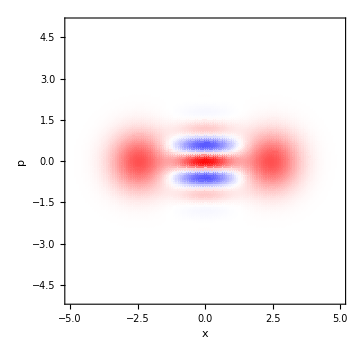
(a) Threshold | (b) Homodyne
-Graphics- | -Graphics-

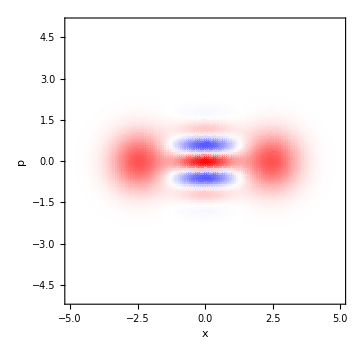
(a) Threshold | (b) Heterodyne
-Graphics- | -Graphics-

```mathematica
ClearAll[η,θ,Δx,Δp];
limits=5;
range=60;
α=2;
θ=0;
Δx=Δp = 0.3;
t =√0.75;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)
r=√(1-t^2);
ηH = 0.85; (* dyne efficiency *)
s=1;

(* Psuccess *)
"Homodyne success probability: "
Re[PsHOM[t,√(1-t^2),α,θ,Δx,ϵHOM[ηH],s]]
"Heterodyne success probability: "
Re[PsHET[t,√(1-t^2),α,θ,Δx,Δp,ϵHET[ηH],s]]


matWnHOM=Table[Re[Chop[WnHOM[t,√(1-t^2),α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,Δx,ϵHOM[ηH],s]]],{p,1,2 range +1},{x,1,2 range +1}];
matWnHOM=matWnHOM/(Abs[ Total[matWnHOM,2]](limits/range)^2);

matWnHET=Table[Re[Chop[WnHET[t,√(1-t^2),α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,Δx,Δp,ϵHET[ηH],s]]],{p,1,2 range +1},{x,1,2 range +1}];
matWnHET=matWnHET/(Abs[ Total[matWnHET,2]](limits/range)^2);

(* numerical fitting with mathematica *)
(*model=WnTHR[t,α,θ,x,p,η,s];
range =(Dimensions[matWnHOM][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,matWnHOM[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{η,0.5}},{p,x}]*)

(* from analytical expressions *)
"Equivalent threshold efficiency for the Homodyne case:"
fitHOM=ηFitHOM[t,r,α,θ,Δx,ϵHOM[ηH],s]
"Equivalent threshold efficiency for the Heterodyne case:"
fitHET=ηFitHET[t,r,α,θ,Δx,Δp,ϵHET[ηH],s]

matWnTHRHOM=Table[Re[Chop[WnTHR[t,α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,Re[η/.fitHOM],s]]],{p,1,2 range +1},{x,1,2 range +1}];
matWnTHRHOM=matWnTHRHOM/(Abs[Total[matWnTHRHOM,2]](limits/range)^2);

matWnTHRHET=Table[Re[Chop[WnTHR[t,α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,Re[η/.fitHET],s]]],{p,1,2 range +1},{x,1,2 range +1}];
matWnTHRHET=matWnTHRHET/(Abs[Total[matWnTHRHET,2]](limits/range)^2);

"Equivalent Threshold success probability for the Homodyne measurement case: "
PsTHR[t,α,Re[η/.fitHOM],s]
"Equivalent Threshold success probability for the Heterodyne measurement case: "
PsTHR[t,α,Re[η/.fitHET],s]

plotTHRHOM=ListDensityPlot[matWnTHRHOM,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(#/Max[{Abs[Max[matWnTHRHOM]],Abs[Min[matWnTHRHOM]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
plotTHRHET=ListDensityPlot[matWnTHRHET,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(#/Max[{Abs[Max[matWnTHRHET]],Abs[Min[matWnTHRHET]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];

plotHOM=ListDensityPlot[matWnHOM,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(#/Max[{Abs[Max[matWnHOM]],Abs[Min[matWnHOM]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
plotHET=ListDensityPlot[matWnHET,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(#/Max[{Abs[Max[matWnHET]],Abs[Min[matWnHET]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
Grid[{{"(a) Threshold","(b) Homodyne"},{plotTHRHOM,plotHOM}}]
Grid[{{"(a) Threshold","(b) Heterodyne"},{plotTHRHET,plotHET}}]
```

```mathematica
(* This ϵ = 2δ = 0 result matches with the ideal homodyne heralding result from Wigner Cat-v2.nb for t=√0.50 *)
```

#### [Obs] Comparing x-Homodyne and Heterodyne methods

As a function cat state angle θ

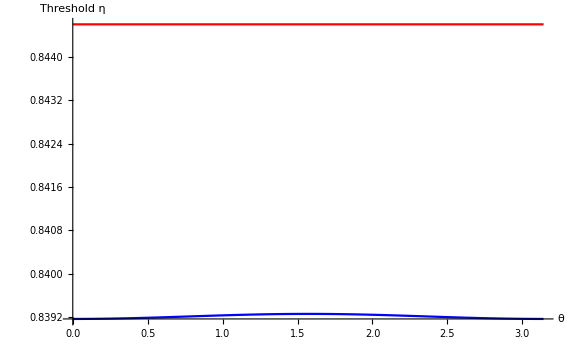

```mathematica
α=2;
Δx=Δp =0.3;
t =√0.75;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)
r=√(1-t^2);
ηH =0.85; (* dyne efficiency *)
s=1;
ClearAll[θ];
Plot[{η/.ηFitHOM[t,r,α,θ,Δx,ϵHOM[ηH],s],η/.ηFitHET[t,r,α,θ,Δx,Δp,ϵHET[ηH],s]},{θ,0,π},AxesLabel->{θ,"Threshold η"},PlotStyle->{Blue,Red},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Large]
```

```mathematica
(* HET gives better efficiency *)
```

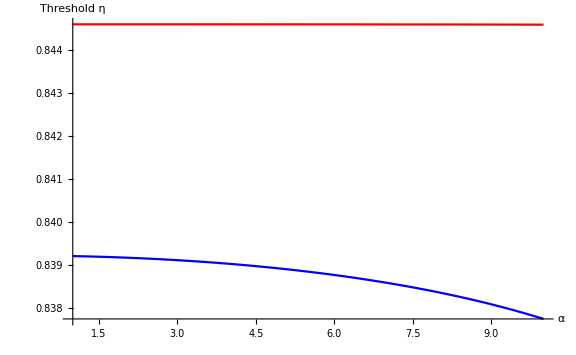

```mathematica
Δx = Δp = 0.3;
t =√0.75;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)
r=√(1-t^2);
ηH = 0.85; (* dyne efficiency *)
s=1;
θ=0;
ClearAll[α];
Plot[{η/.ηFitHOM[t,r,α,θ,Δx,ϵHOM[ηH],s],η/.ηFitHET[t,r,α,θ,Δx,Δp,ϵHET[ηH],s]},{α,1,10},AxesLabel->{α,"Threshold η"},PlotStyle->{Blue,Red},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Large]
```

```mathematica
(* η doesn't seem to depend on α for HET.  *)
```

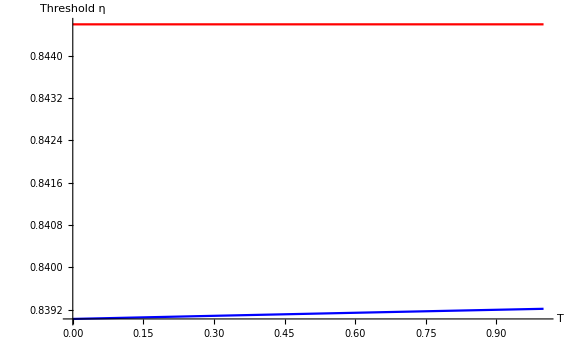

```mathematica
Δx = Δp = 0.3;
t =√0.75;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)
r=√(1-t^2);
ηH = 0.85; (* dyne efficiency *)
s=1;
α=2;
θ=0;
ClearAll[T];
Plot[{η/.ηFitHOM[√T,√(1-T),α,θ,Δx,ϵHOM[ηH],s],η/.ηFitHET[√T,√(1-T),α,θ,Δx,Δp,ϵHET[ηH],s]},{T,0,1},AxesLabel->{T,"Threshold η"},PlotStyle->{Blue,Red},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Large]
```

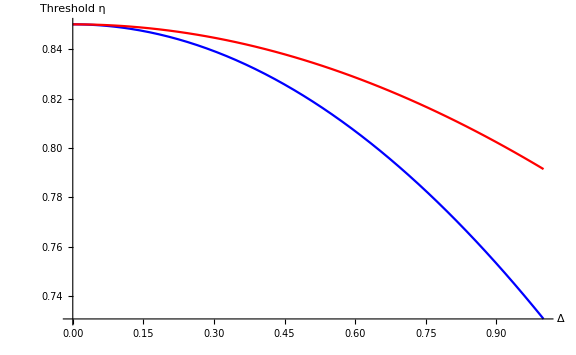

```mathematica
ClearAll[t,r,α,θ,Δ,s];
t =√0.75;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)
r=√(1-t^2);
ηH =0.85; (* dyne efficiency *)
s=1;
α=2;
θ=0;

Plot[{η/.ηFitHOM[t,r,α,θ,Δ,ϵHOM[ηH],s],η/.ηFitHET[t,r,α,θ,Δ,Δ,ϵHET[ηH],s]},{Δ,0,1},AxesLabel->{Δ,"Threshold η"},PlotStyle->{Blue,Red},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Large]
```

```mathematica
(* HET is better for any given Δ *)
```

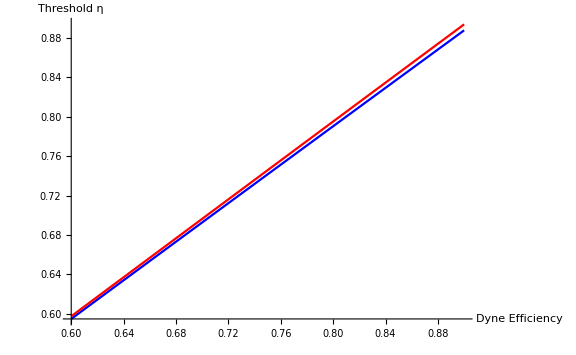

```mathematica
ClearAll[t,r,α,θ,Δ,s,η];
t =√0.75;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)
r=√(1-t^2);
s=1;
α=2;
θ=0;
Δ =0.3;
Plot[{η/.ηFitHOM[t,r,α,θ,Δ,ϵHOM[ηH],s],η/.ηFitHET[t,r,α,θ,Δ,Δ,ϵHET[ηH],s]},{ηH,0.6,0.9},AxesLabel->{"Dyne Efficiency","Threshold η"},PlotStyle->{Blue,Red},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Large]
```

#### [Rslt] When is it definitely better to Heterodyne compared to Thresholding? When the success prob is better.

Dyne efficiency chosen:

0.85

HOMODYNE:
 
* Equivalence point:

{η→0.733959+0. ⅈ,Δ→0.986858+0. ⅈ}

* RO and RI plots:

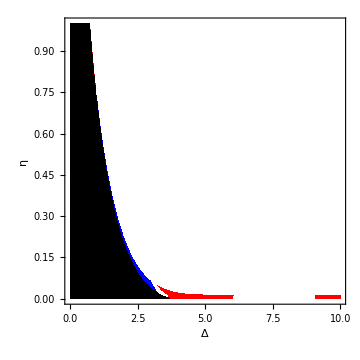

HETERODYNE:
 
* Equivalence point:

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{η→1.50573×10^-9+0. ⅈ,Δ→15.6925+0. ⅈ}

* RO and RI plots:

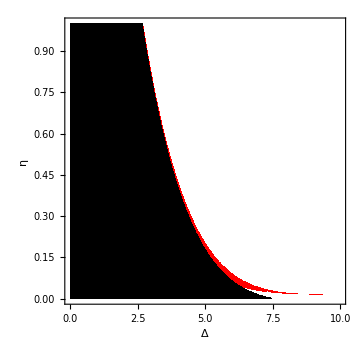

```mathematica
(* Plotting overlap and prob. improvement plots on top of each other. Intersecting lines mean that heterodyning is better to simulate certain efficiencies. Observation: α needs to be sufficienctly small. But be wary that too small α means we need bigger Δ. *)
ClearAll[α,θ,t,r,s,plotpoints,Δ];
t=√0.75;
r=√(1-t^2);
θ=0;
α=2;
s=1;
"Dyne efficiency chosen:"
ηH =0.85
plotpoints=60;

"HOMODYNE:
 
* Equivalence point:"
EquivalencePointHOM[t,r,α,θ,ϵHOM[ηH],s]
"* RO and RI plots:"
plotROHOM = DensityPlot[HeavisideTheta[Re[ηRelativeOverlapHOM[t,r,α,θ,Δ,ϵHOM[ηH],η,s]]],{Δ,0,10},{η,0,1},PlotPoints->plotpoints,ColorFunction->(Blend[{RGBColor[0,0,1,1],RGBColor[1,0,0,1]},#]&),ColorFunctionScaling->False,PlotRange->All,FrameLabel->{Δ,η},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},ImageSize->Medium];
plotRIHOM=DensityPlot[HeavisideTheta[Re[PsηRelativeImprovementHOM[t,r,α,θ,Δ,ϵHOM[ηH],η,s]]],{Δ,0,10},{η,0,1},PlotPoints->plotpoints,ColorFunction->(Blend[{RGBColor[0,0,0,0.3],RGBColor[1,1,1,0.3]},#]&),ColorFunctionScaling->False,PlotRange->All,FrameLabel->{Δ,η},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},ImageSize->Medium];
Show[{plotROHOM,plotRIHOM}]

"HETERODYNE:
 
* Equivalence point:"
EquivalencePointHET[t,r,α,θ,ϵHET[ηH],s]
"* RO and RI plots:"
plotROHET = DensityPlot[HeavisideTheta[Re[ηRelativeOverlapHET[t,r,α,θ,Δ,Δ,ϵHET[ηH],η,s]]],{Δ,0,10},{η,0,1},PlotPoints->plotpoints,ColorFunction->(Blend[{RGBColor[0,0,1,1],RGBColor[1,0,0,1]},#]&),ColorFunctionScaling->False,PlotRange->All,FrameLabel->{Δ,η},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},ImageSize->Medium];
plotRIHET=DensityPlot[HeavisideTheta[Re[PsηRelativeImprovementHET[t,r,α,θ,Δ,Δ,ϵHET[ηH],η,s]]],{Δ,0,10},{η,0,1},PlotPoints->plotpoints,ColorFunction->(Blend[{RGBColor[0,0,0,0.3],RGBColor[1,1,1,0.3]},#]&),ColorFunctionScaling->False,PlotRange->All,FrameLabel->{Δ,η},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},ImageSize->Medium];
Show[{plotROHET,plotRIHET}]

ClearAll[α,θ,t,r,s,plotpoints];
```

#### [Obs]

HET doesn’t seem to depend on α very strongly or beam splitter transmittance T which is strange. Its independence from θ makes sense though as we measure both x and p.
“Equivalence point” which is where the success prob of threshold is equal to success prob of dyning occurs close to zero efficiency --- numerically. 
This means whenever we have sufficiently efficient threshold detectors available, we should prefer those. 
However, the situation much more interesting in the Homodyne case.